```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
```

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
alpha[r_,k_,l_,h_]:=(1+h (D[FunctionExpand[RiccatiBesselN[k x,l]],x]/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
beta[r_,k_,l_,h_]:=h FunctionExpand[RiccatiBesselJ[k r,l]](((D[FunctionExpand[RiccatiBesselJ[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselJ[k r,l]])-((D[FunctionExpand[RiccatiBesselN[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV],

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a0_?NumberQ,cfg0_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Switch[cfg0
,{3,1},
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a0]-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
Wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a0,Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 
,{2,1},
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-TwoMyOverHBsq VlocDF[i hDif,lam,c0,d0,a0]-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
Wmat=Table[-hDif^3 TwoMyOverHBsq WnolocDF[i hDif,j hDif,energyMeV,lam,c0,d0,a0,Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}];
,{2,2},
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-TwoMyOverHBsq VlocDD[i hDif,lam,c0,d0,a0]-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
Wmat=Table[-hDif^3 TwoMyOverHBsq WnolocDD[i hDif,j hDif,energyMeV,lam,c0,d0,a0,Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}];
];

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

Amat=Dmat+Kmat+Wmat;

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

wf=Table[{i hDif,usol⟦i⟧},{i,1,Npoints}];
tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

```mathematica
(* Nuclear E2=2.22 E3=8.48 *)
LEC={(*{0.16,1,-5.23609711,-0.2508527567},{0.2,1,-6.21155090,-0.01411577035},{0.3,1,-9.04089890,0.9058334635},{0.35,1,-10.66481819,1.562725218},{0.4,1,-12.42824554,2.36543082},{0.45,1,-14.33104515,3.3244409},{0.5,1,-16.37322998,4.450396189},{0.55,1,-18.55475197,5.753778748},{0.6,1,-20.87557983,7.245120228},{0.65,1,-23.33569527,8.935015304},{0.7,1,-25.93508911,10.83416803},{0.75,1,-28.67371368,12.95315533},{0.8,1,-31.55156555,15.30282946},{0.85,1,-34.56868362,17.89442822},{0.9,1,-37.72501221,20.7388847},{0.95,1,-41.02048416,23.84721094},*)
{1.00,1,-44.45520020,27.2312836},
{1.05,1,-48.02915573,30.9028667},
{1.10,1,-51.74223328,34.8734185},
{1.20,1,-59.58599854,43.7610139},
{1.50,1,-86.45745087,78.9169705},
{2.00,1,-142.3761444,172.703829},   (*B3=8.47*)
{3.00,1,-295.9593505,559.013463},
{4.00,1,-505.2016601,1397.56945},
{6.00,1,-1090.628800,6311.30367}  (*B3=8.467*)
(*{10.0,1,-2933.556400,89436.1852}*)};(* B2>2.22 B3=8.467*)
(*{14.0,1,-5676.297200,144399.039}*) (*B3=13.xx*)
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for DIMER-DIMER (AB-AB)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
Vc[r_,lam_,Cc_]:=Cc Exp[-lam r^2];

VlocDD[r_,lam_,Cc_,Dd_,Aa_]:=Block[{eta,w},
eta=2 Cc (2 Aa/(2 Aa+lam))^(3/2);
w=(2 Aa lam/(2 Aa+lam));
 eta Exp[-w r^2]
];

WnolocDD[r_,rp_,e_,lam_,Cc_,Dd_,Aa_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,a1,b1,c1,a2,b2,c2},
zeta1=8 Aa^(3/2) 1/TwoMyOverHBsq;
zeta2=-16 Aa^(3/2) Cc (2 Aa/(2 Aa+lam))^(3/2);
a1=Aa;c1=a1;
a2=Aa (2 Aa+3 lam)/(2 Aa+lam);
c2=Aa;
-(4 Pi r rp) (
 zeta1 Exp[-a1 r^2-c1 rp^2] (-(4 (a1)^2 r^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq e) I^Ll KroneckerDelta[Ll,0]
+I^Ll zeta2 KroneckerDelta[Ll,0] Exp[-a2 r^2-c2 rp^2]
)
];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for DIMER-FERMION (AB-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
VlocDF[r_,lam_,Cc_,Dd_,Aa_]:=Block[{eta,w},
eta=8 Cc (Aa/(4 Aa+lam))^(3/2);
w=4 Aa lam/(4 Aa+lam);
eta Exp[-w r^2]
];

WnolocDF[r_,rp_,e_,lam_,Cc_,Dd_,Aa_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,a1,b1,c1,a2,b2,c2},
zeta1=(64/27) (2 Aa)^(3/2) 1/TwoMyOverHBsq;
zeta2=-(64/27) (2 Aa)^(3/2) Cc;
a1=(10/9) Aa;c1=a1;
b1=(16/9) Aa;
a2=(2/9) (5 Aa+8 lam);c2=(2/9) (5 Aa+2 lam);
b2=(16/9) (Aa+lam);
-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 (a1)^2 r^2+(b1)^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq e) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}]
)
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
)];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
VlocTF[r_,lam_,Cc_,Dd_,Aa_]:=Block[{eta2,eta3,w2,w3},
eta2=2 Cc (3 Aa/(3 Aa+lam))^(3/2);
w2=3 Aa lam/(3 Aa+lam);
eta3=8 Dd (3 Aa^2/(12 Aa^2+16 Aa lam+lam^2))^(3/2);
w3=(12 Aa lam (Aa+lam)/(12 Aa^2+16 Aa lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27/8)(3/2 Aa)^(3/2) (1./TwoMyOverHBsq);
a1=(Aa 15/16);
b1=(Aa 18/16);
c1=a1;

zeta2=-2 27 (Aa 3/2)^(3./2) Cc (Aa/(4 Aa+lam))^(3/2);
zeta3=-27 (Aa 3/2)^(3./2) Dd (Aa/(4 Aa+5 lam))^(3/2);

a2=3 Aa (5 Aa+8 lam)/(4 (4 Aa+lam));
b2=9 Aa (Aa+lam)/(2 (4 Aa+lam));
c2=3 Aa (5 Aa+2 lam)/(4 (4 Aa+lam));

a3=3 (20 Aa^2+52 Aa lam+27 lam^2)/(4 (16 Aa+20 lam));
b3=9 (4 Aa^2+8 Aa lam+3 lam^2)/(2 (16 Aa+20 lam));
c3=3 (20 Aa^2+28 Aa lam+3 lam^2)/(4 (16 Aa+20 lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 (r^2+rp^2)] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

scattering length

a_l=-(tan δ_l(k))/k^(2l+1)

```mathematica
nGrid=250;
cfg={3,1};
k0FM=0.01;
Switch[cfg[[1]],
2,afit=6.;rr=30,
3,afit=2.;rr=30; 
];
hbar=197.327053;
Mm=938.92;
m1=cfg[[1]] Mm;m2=cfg[[2]] Mm;
μ=m1 m2/(m1+m2);mh2=(2 μ)/(hbar)^2;
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV"]
λRange=Range[Length[LEC]-1,Length[LEC]];
```

E_0 = 0.00276473 MeV

```mathematica
nn=3;
ee=1.09;
rp=0.1;
Lrel=1;
Animate[
Plot[
{VlocTF[R,LEC[[nn]][[1]],fC LEC[[nn]][[3]],fD LEC[[nn]][[4]],AA],Re[WnolocTF[R,rp,EE,LEC[[nn]][[1]],fC LEC[[nn]][[3]],fD LEC[[nn]][[4]],AA,Lrel,mh2]]},{R,0.01,5.0},PlotPoints->40,MaxRecursion->0,PlotLegends->{"V_local","V_(non - local)"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black}},AxesLabel->{"R [fm]"},PlotLabel->{"A="<>ToString[cfg]<>"  Λ = "<>ToString[LEC[[nn]][[1]]]<>"fm^-1"},PlotRange->Full]
,{AA,0.5,1.82,Appearance->"Labeled"}
,{EE,0.00005,30.1,Appearance->"Labeled"}
,{fC,0.5,10,Appearance->"Labeled"}
,{fD,0.5,10,Appearance->"Labeled"}
,DefaultDuration->3,AnimationRepetitions->2,AnimationRunning->False]

Plot3D[Re[WnolocTF[rr,rp,0.0001,LEC[[nn]][[1]],LEC[[nn]][[3]],LEC[[nn]][[4]],0.6,Lrel,mh2]],{rr,0.01,4.0},{rp,0.01,4.0},PlotRange->Full]
```

-Graphics3D-

S-wave phase shifts -- basics first

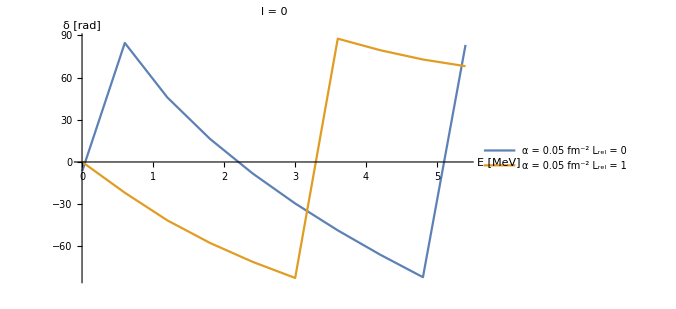

```mathematica
Lrel=0;
rr=15;
nn=Length[LEC]-4;
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=6.78 LEC⟦nn⟧[[3]];D0=12 LEC⟦nn⟧[[4]];
α0=.2 afit^(-2);
dE=0.6;
ErangeMeV=Range[(k0FM hbar)^2/(2 μ),6.0,dE];

nGrid=100;

tanDs={};tanDp={};
SetSharedVariable[tanDs,tanDp];
ParallelDo[
momFM=Sqrt[2 μ ee]/hbar;
TanDelSwave=Chop[SolveSecular[rr,nGrid,momFM,0,λ,C0,D0,α0,cfg,mh2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,momFM,1,λ,C0,D0,α0,cfg,mh2]];
AppendTo[tanDs,{ee,TanDelSwave}];
AppendTo[tanDp,{ee,TanDelPwave}];
,{ee,ErangeMeV}];

tnDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]];
tnDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]];
phaseS=Transpose[{tnDs[[All,1]],180./Pi ArcTan[tnDs[[All,2]]]}];
phaseP=Transpose[{tnDp[[All,1]],180./Pi ArcTan[tnDp[[All,2]]]}];
leg="α = "<>ToString[α0]<>" fm^-2    L_rel = "<>ToString[#]&/@{0,1};
ListPlot[{phaseS,phaseP},AxesLabel->{"E [MeV]","δ [rad]"},ImageSize->500,PlotLegends->leg,PlotRange->Automatic,Joined->True,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
```

S-wave scattering length -- used to calibrate α

we chose the singlet value a_s≈4±1fm (3-1) and a_s≈6±0.2fm (2-1) to ensure calibrate the α core parameter of the triton and deuteron;
(cf. https://arxiv.org/pdf/1105.3763.pdf )

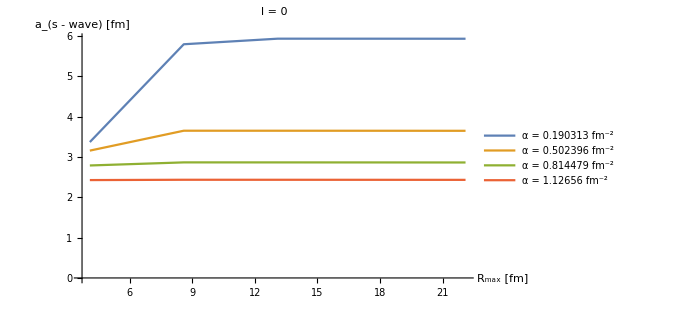

```mathematica
Lrel=0;
aOfa={};
αRange=Subdivide[2.03 3/2 afit^(-2),36.05/2 afit^(-2),3];
rRange=Subdivide[4.1,22.1,4];
k0FM=0.01;
nGrid=200;
Do[
aS={};
SetSharedVariable[aS];
nn=Length[LEC]-2;
ParallelDo[
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];
TanDelSwave=Chop[SolveSecular[rr,nGrid,k0FM,0,λ,C0,D0,α0,cfg,mh2]];
AppendTo[aS,{rr,-TanDelSwave/k0FM^(2 Lrel+1)}];
,{rr,rRange}];
a0=Reverse[Sort[aS,#1[[1]]>#2[[1]]&]];
AppendTo[aOfa,a0];
,{α0,αRange}];
leg="α = "<>ToString[#]<>" fm^-2"&/@αRange;
ListPlot[aOfa,AxesLabel->{"R_max [fm]","a_(s - wave) [fm]"},ImageSize->500,PlotLegends->leg,PlotRange->Automatic,Joined->True,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
```

α-fitting

```mathematica
rr=20;
αL={};
SetSharedVariable[αL];
Lrel=0;
aini=8.1 (3./2.) afit^(-2);

ParallelDo[
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];
alfL=FindRoot[Chop[SolveSecular[rr,nGrid,k0FM,Lrel,λ,C0,D0,alf,cfg,mh2]]==(-k0FM afit),{alf,aini},PrecisionGoal->4];
Print["λ = ",λ," : ",Chop[alf/.alfL]];
AppendTo[αL,{λ,alf/.Chop[alfL]}];
,{nn,λRange}];
αL=Sort[αL];
Put[αL,LocalObject[ToString[cfg[[1]]]<>"-1_CorePara"]]
```

λ = 4. : 1.6665

λ = 9. : 1.66662

LocalObject[file:///home/kirscher/.Wolfram/Objects/3-1_CorePara]

S-matrix pole (S-wave)

```mathematica
dE=0.5;
ErangeMeV=Range[(k0FM hbar)^2/(2 μ),41.0,dE];
Put[ErangeMeV,LocalObject["ErangeMeVS"]];
αL=Get[LocalObject[ToString[cfg[[1]]]<>"-1_CorePara"]];

Lrel=0;

data={};
Do[
Xl={};
SetSharedVariable[Xl];
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];α0=Select[αL,#[[1]]==λ&][[1]][[2]];

Print["λ="<>ToString[λ]<>"fm^-2  ;   α="<>ToString[α0]<>"fm^-2"];

ParallelDo[
momFM=(2 μ En/hbar^2)^0.5;
TanDel=Chop[SolveSecular[rr,nGrid,momFM,Lrel,λ,C0,D0,α0,cfg,mh2]];
AppendTo[Xl,{En,((2 μ En)^(Lrel+0.5))/TanDel}];
,{En,ErangeMeV}];

Xlr=Reverse[Sort[Xl,#1[[1]]>#2[[1]]&]];
AppendTo[data,{λ,Xlr}];

,{nn,λRange}]
Put[data,LocalObject["Swave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_TanDelta"]]
```

λ=4.fm^-2  ;   α=1.6665fm^-2

λ=9.fm^-2  ;   α=1.66662fm^-2

LocalObject[file:///home/kirscher/.Wolfram/Objects/Swave_3-1_TanDelta]

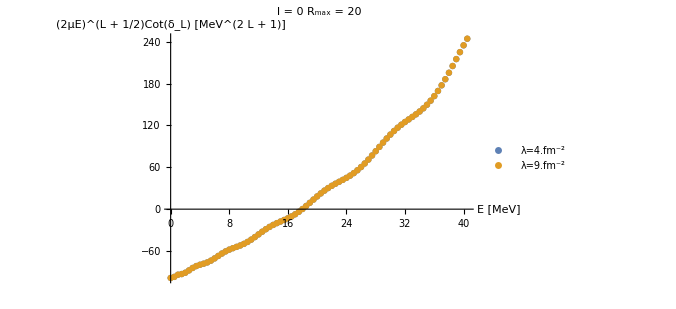

```mathematica
data=Get[LocalObject["Swave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_TanDelta"]];
legs="λ="<>ToString[#[[1]]]<>"fm^-2"&/@data;
ListPlot[data[[All,2]],AxesLabel->{"E [MeV]","(2μE)^(L + 1/2)Cot(δ_L) [MeV^(2  L + 1)]"},ImageSize->500,PlotLegends->legs,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel]<>"   R_max = "<>ToString[rr],Orange,16]]
```

Kukulin, Theory of Resonances, ch.6.1.1 Eq.(1.1) ff      S_l(k)=Numerator/(k^(2l+1)cotδ_l-ik^(2l+1))      →_(k→0)        Numerator/(-a_l^-1+1/2 r_l k^2+O(k^4)-ik^(2l+1))
Pade (typeII): X_l(k^2)=(P_N^(l)(k^2))/(Q_M^(l)(k^2))=(p_0+p_1 z+p_2 z^2+p_3 z^3+…)/(1+q_1 z+q_2 z^2+q_3 z^3+…):=k^(2l+1)cotδ_l=-1/a_l+1/2 r_l k^2-1/4 P_l k^4+…  

⇒   S_l(k)=(P_N^(l)(k^2) + ik^(2l+1)Q_M^(l)(k^2))/(P_N^(l)(k^2) - ik^(2l+1)Q_M^(l)(k^2))    ⇒     P_N^(l)(k_res^2)-ik_res^(2l+1)Q_M^(l)(k_res^2)=0

-Graphics-

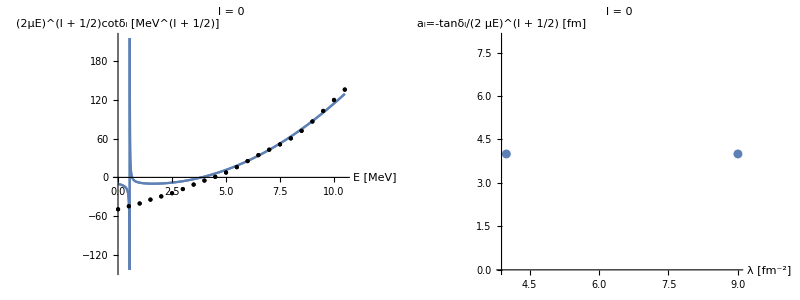

```mathematica
data=Get[LocalObject["Swave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_TanDelta"]];
ErangeMeV=Get[LocalObject["ErangeMeVS"]];
Poles={};PadeSolus={};Lrel=0;

PadeOrderN=3;PadeOrderM=1;

Do[
Clear[coffs];
coffs={Array[cn,PadeOrderN+1],Array[cm,PadeOrderM]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{-0.01,1.2},Length[Flatten[coffs]]]}];
constr=10^1>#>-10^1&/@Flatten[coffs];
Union[constr,{}];

PadePolyP=coffs[[1]][[PadeOrderN+1]]+Sum[coffs[[1]][[i]] ee^i,{i,1,PadeOrderN}];
PadePolyQ=1+Sum[coffs[[2]][[i]] ee^i,{i,1,PadeOrderM}];
modelX=PadePolyP/PadePolyQ;

efitmax=Position[Table[If[data[[n]][[2]][[nn]][[2]]<data[[n]][[2]][[nn+1]][[2]],data[[n]][[2]][[nn]],"42"],{nn,Range[Length[data[[n]][[2]]]-1]}],"42"];
If[efitmax=={},efitmax=Length[data[[n]][[2]]],efitmax=Flatten[efitmax][[1]]];
fitdata=data[[n]][[2]][[;;efitmax]];

solu=FindFit[fitdata,{modelX,constr},Flatten[coffs],ee,MaxIterations->500];

poles=Solve[((PadePolyP/PadePolyQ-I (2 μ ee)^(Lrel+0.5))/.solu)==0,ee];

(*Print["λ = ",data[[n]][[1]],"   : E_pole = ",poles];(*,"   ",solu];*)*)
AppendTo[Poles,Transpose[{Table[data[[n]][[1]],Length[poles]],Flatten[ee/.poles]}]];
AppendTo[PadeSolus,{data[[n]][[1]],solu}];
,{n,Range[Length[data]]}]

tmp=Transpose[{#[[1]]&/@Flatten[Poles,1],Re[#[[2]]]&/@Flatten[Poles,1],Im[#[[2]]]&/@Flatten[Poles,1]}];
Export[NotebookDirectory[]<>"pole_data_Swave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>".dat",tmp,"Table","FieldSeparators"->"    "];
Poland=Transpose[{Flatten[Poles,1][[All,1]],Flatten[Poles,1][[All,2]]}];
PolandRe=Re[Poland];
PolandIm=Transpose[{Flatten[Poles,1][[All,1]],Im[Flatten[Poles,1][[All,2]]]}];
cplxpoles=Transpose[{Re[Poland[[All,2]]],Im[Poland[[All,2]]]}];
Grid[{{ListPlot[PolandRe,AxesLabel->{"λ [fm^-2]","Re[E_res] [MeV]"},ImageSize->500,PlotRange->Automatic],
ListPlot[PolandIm,AxesLabel->{"λ [fm^-2]","Im[E_res] [MeV]"},ImageSize->500,PlotRange->Automatic],
ListPlot[cplxpoles->Poland[[All,1]],PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"Re[E_res] [MeV]","Im[E_res] [MeV]"},ImageSize->500]}}]
Grid[{{Plot[(modelX/.#[[2]]/.ee->em)&/@PadeSolus,{ee,ErangeMeV[[1]],ErangeMeV[[-1]]},AxesLabel->{"E [MeV]","(2μE)^(l + 1/2)cotδ_l [MeV^(l + 1/2)]"},ImageSize->500,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16],Epilog->Map[Point,#[[2]]&/@data]],
ListPlot[Transpose[{data[[All,1]],-hbar/#[[2]][[1]][[2]]&/@data}],AxesLabel->{"λ [fm^-2]","a_l=-tanδ_l/(2  μE)^(l + 1/2) [fm]"},ImageSize->500,PlotRange->Full,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
}}]
```

P-wave

here we assess the convergence of the integration with box size (rr)
ECCE: for d-d, the non-local potential is zero in accordance with the symmetric exchange of the bose particle (AB); the remaining
             local interaction goes to zero for  λ → ∞; therefore, the free solution exhibits a strong box-size dependence

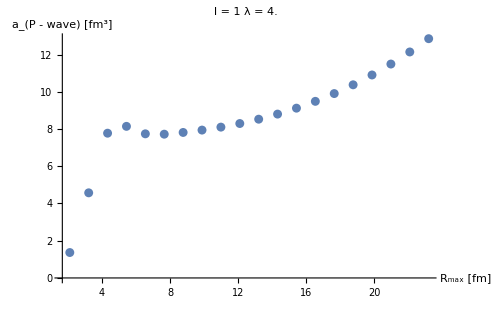

```mathematica
αL=Get[LocalObject[ToString[cfg[[1]]]<>"-1_CorePara"]];
Lrel=1;
rRange=Subdivide[2.1,23.2,19];

aP={};
SetSharedVariable[aP];

nn=8;(*Length[LEC];*)
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];α0=Select[αL,#[[1]]==λ&][[1]][[2]];

ParallelDo[
TanDelPwave=Chop[SolveSecular[rr,nGrid,k0FM,Lrel,λ,C0,D0,α0,cfg,mh2]];
AppendTo[aP,{rr,-TanDelPwave/k0FM^(2 Lrel+1)}];
,{rr,rRange}];

a1=Reverse[Sort[aP,#1[[1]]>#2[[1]]&]];

leg="α = "<>ToString[α0]<>" fm^-2";
ListPlot[a1,AxesLabel->{"R_max [fm]","a_(P - wave) [fm^3]"},ImageSize->500,PlotLegends->leg,PlotRange->Full,PlotLabel->Style["l = "<>ToString[Lrel]<>"   λ = "<>ToString[λ],Orange,16]]
```

S-matrix pole (P-wave)

```mathematica
αL=Get[LocalObject[ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_CorePara"]];
nGrid=100;
ErangeMeV=Range[(k0FM hbar)^2/(2 μ),25.0,1];
Put[ErangeMeV,LocalObject["ErangeMeVP"]];
rr=10;
Lrel=1;

data={};
Do[
Xl={};
SetSharedVariable[Xl];
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];
α0=Select[αL,#[[1]]==λ&][[1]][[2]];
Print["λ="<>ToString[λ]<>"fm^-2  ;   α="<>ToString[α0]<>"fm^-2"];

ParallelDo[
momFM=(2 μ En/hbar^2)^0.5;
TanDel=Chop[SolveSecular[rr,nGrid,momFM,Lrel,λ,C0,D0,α0,cfg,mh2]];
AppendTo[Xl,{momFM,(momFM^(2 Lrel+1))/TanDel}];
,{En,ErangeMeV}];

Xlr=Reverse[Sort[Xl,#1[[1]]>#2[[1]]&]];
AppendTo[data,{λ,Xlr}];
,{nn,λRange}]
Put[data,LocalObject["Pwave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_TanDelta"]]
```

λ=4.fm^-2  ;   α=0.417391fm^-2

λ=9.fm^-2  ;   α=0.416324fm^-2

LocalObject[file:///home/kirscher/.Wolfram/Objects/Pwave_3-1_TanDelta]

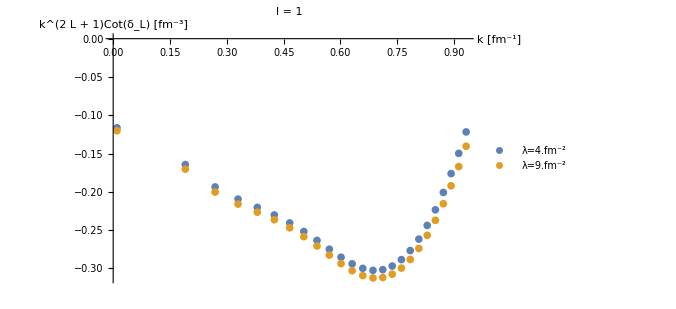

```mathematica
data=Re[Get[LocalObject["Pwave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_TanDelta"]]];
legs="λ="<>ToString[#[[1]]]<>"fm^-2"&/@data;
ListPlot[data[[All,2]],AxesLabel->{"k [fm^-1]","k^(2  L + 1)Cot(δ_L) [fm^-3]"},ImageSize->500,PlotLegends->legs,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
```

Kukulin, Theory of Resonances, ch.6.1.1 Eq.(1.1) ff      S_l(k)=Numerator/(k^(2l+1)cotδ_l-ik^(2l+1))      →_(k→0)        Numerator/(-a_l^-1+1/2 r_l k^2+O(k^4)-ik^(2l+1))
Pade (typeII): X_l(k)=(P_N^(l)(k^2))/(Q_M^(l)(k^2)):=k^(2l+1)cotδ_l  ⇒   S_l(k)=(P_N^(l)(k^2) + ik^(2l+1)Q_M^(l)(k^2))/(P_N^(l)(k^2) - ik^(2l+1)Q_M^(l)(k^2))    ⇒     P_N^(l)(k_res^2)-ik_res^(2l+1)Q_M^(l)(k_res^2)=0

FindFit::sdir: Search direction has become too small.

-Graphics-

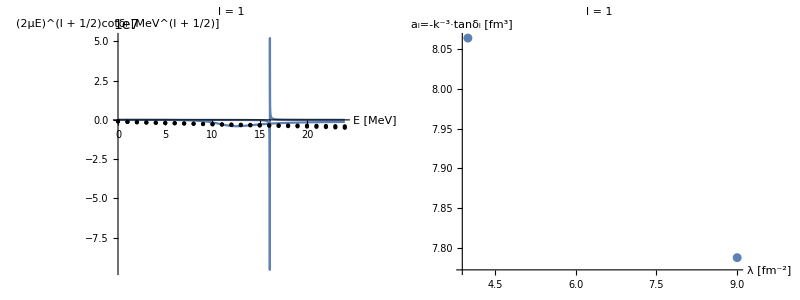

```mathematica
data=Re[Get[LocalObject["Pwave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_TanDelta"]]];
ErangeMeV=Get[LocalObject["ErangeMeVP"]];

Poles={};PadeSolus={};Lrel=1;

PadeOrderN=3;PadeOrderM=2;

Do[
Clear[coffs];
coffs={Array[cn,PadeOrderN+1],Array[cm,PadeOrderM]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{-0.01,0.2},Length[Flatten[coffs]]]}];
constr=10^2>#>-10^2&/@Flatten[coffs];
Union[constr,{}];

PadePolyP=coffs[[1]][[PadeOrderN+1]]+Sum[coffs[[1]][[i]] ee^i,{i,1,PadeOrderN}];
PadePolyQ=1+Sum[coffs[[2]][[i]] ee^i,{i,1,PadeOrderM}];
modelX=PadePolyP/PadePolyQ;

dati=data[[n]][[2]][[All,2]];
(*efitmax=Position[Table[If[data[[n]][[2]][[nn]][[2]]<data[[n]][[2]][[nn+1]][[2]],data[[n]][[2]][[nn]],"42"],{nn,Range[Length[data[[n]][[2]]]-1]}],"42"];*)
efitmax=Position[Differences[dati,1],Max[Differences[dati,1]]][[1]][[1]];
If[efitmax=={},efitmax=Length[data[[n]][[2]]],efitmax=Flatten[efitmax][[1]]];
fitdata=data[[n]][[2]][[;;efitmax]];

solu=FindFit[fitdata,{modelX,constr},Flatten[coffs],ee,MaxIterations->500];

poles=Solve[((modelX-I (2 μ ee)^(Lrel+0.5))/.solu)==0,ee];

(*Print["λ = ",data[[n]][[1]],"   : E_pole = ",poles];(*,"   ",solu];*)*)
AppendTo[Poles,Transpose[{Table[data[[n]][[1]],Length[poles]],Flatten[ee/.poles]}]];
AppendTo[PadeSolus,{data[[n]][[1]],solu}];
,{n,Range[Length[data]]}]

tmp=Transpose[{#[[1]]&/@Flatten[Poles,1],Re[#[[2]]]&/@Flatten[Poles,1],Im[#[[2]]]&/@Flatten[Poles,1]}];
Export[NotebookDirectory[]<>"pole_data_Pwave_"<>ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>".dat",tmp,"Table","FieldSeparators"->"    "];
Poland=Transpose[{Flatten[Poles,1][[All,1]],Flatten[Poles,1][[All,2]]}];
PolandRe=Re[Poland];
PolandIm=Transpose[{Flatten[Poles,1][[All,1]],Im[Flatten[Poles,1][[All,2]]]}];
cplxpoles=Transpose[{Re[Poland[[All,2]]],Im[Poland[[All,2]]]}];
Grid[{{ListPlot[PolandRe,AxesLabel->{"λ [fm^-2]","Re[E_res] [MeV]"},ImageSize->500,PlotRange->Automatic],
ListPlot[PolandIm,AxesLabel->{"λ [fm^-2]","Im[E_res] [MeV]"},ImageSize->500,PlotRange->Automatic],
ListPlot[cplxpoles->Poland[[All,1]],PlotRange->Full,AxesLabel->{"Re[E_res] [MeV]","Im[E_res] [MeV]"},ImageSize->500]}}]
Grid[{{Plot[(modelX/.#[[2]]/.ee->em)&/@PadeSolus,{ee,ErangeMeV[[1]],ErangeMeV[[-1]]},AxesLabel->{"E [MeV]","(2μE)^(l + 1/2)cotδ_l [MeV^(l + 1/2)]"},ImageSize->500,PlotRange->Full,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16],Epilog->Map[Point,#[[2]]&/@data]],
ListPlot[Transpose[{data[[All,1]],-hbar^(2 Lrel+1)/#[[2]][[1]][[2]]&/@data}],AxesLabel->{"λ [fm^-2]","a_l=-k^-3·tanδ_l [fm^3]"},ImageSize->500,PlotRange->Full,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
}}]
```

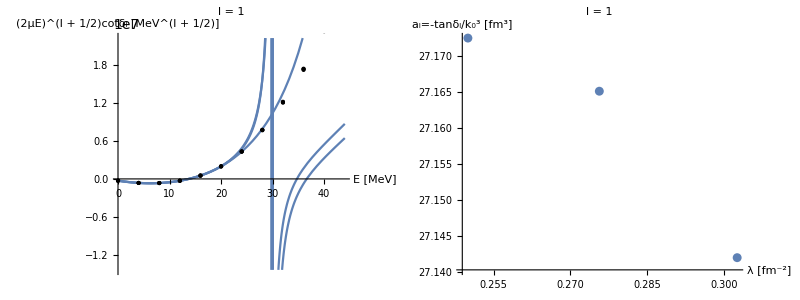

```mathematica
Grid[{{Plot[(#[[2]][[-1]]/.ee->em)&/@SoleSet,{ee,ErangeMeV[[1]],ErangeMeV[[-1]]},AxesLabel->{"E [MeV]","(2μE)^(l + 1/2)cotδ_l [MeV^(l + 1/2)]"},ImageSize->500,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16],Epilog->Map[Point,#[[2]]&/@data]],
ListPlot[Transpose[{data[[All,1]],-hbar^(2 Lrel+1)/#[[2]][[1]][[2]]&/@data}],AxesLabel->{"λ [fm^-2]","a_l=-tanδ_l/k_0^3 [fm^3]"},ImageSize->500,PlotRange->Full,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
}}]
```

S-wave scattering length limit cycle

assume C_nn∝λ^2 and set D_nnn=0

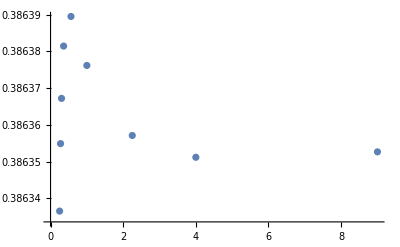

```mathematica
αL=Get[LocalObject[ToString[cfg[[1]]]<>"-"<>ToString[cfg[[2]]]<>"_CorePara"]];
ListPlot[αL]
```

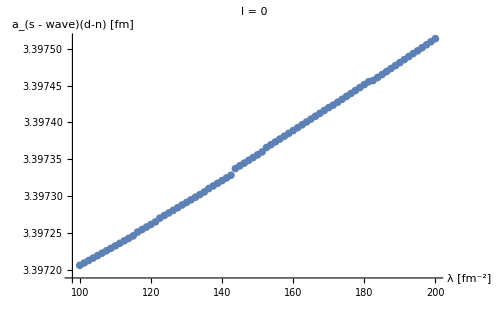

```mathematica
nGrid=300;
Lrel=0;
aOfa={};
rr=40;
α0=1.2;

λRange=Subdivide[100,200,80];


aS={};
SetSharedVariable[aS];

ParallelDo[
TanDelSwave=Chop[SolveSecular[rr,nGrid,k0FM,0,λ,-100 λ,0.0,α0,cfg,mh2]];
AppendTo[aS,{λ,-TanDelSwave/k0FM}];
,{λ,λRange}];

a0=Reverse[Sort[aS,#1[[1]]>#2[[1]]&]];

ListPlot[a0,AxesLabel->{"λ [fm^-2]","a_(s - wave)(d-n) [fm]"},ImageSize->500,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
```